## Глава 1. Элементы теории функций комплексной переменной и её интерпретация в среде Mathematica

## §1. Элементарные функции

### 1.1. Понятие функций комплексной переменной и применение средств Wolfram Mathematica для работы с ними.

Множество точек E расширенной комплексной плоскости (z)=ℂ∪{∞} называется связным, если любые две его точки можно соединить непрерывной кривой, все точки которой принадлежат данному множеству. Связное открытое множество точек комплексной плоскости называется областью и обазнается через D, G  т.п. Область D называется односвязной, если ее граница является связным множеством: в противном случае область D называется многосвязной.
Если каждому комплексному числу z, принадлежащему области D, поставлено в соответствие некоторое комплексное число w, то говорят, что в области D определена комплексная функция w =  f(z).

Пусть z=x+ⅈ y и w=u+ⅈ v. Тогда функция w =  f(z) может быть представлена с помощью двех действительных функций  u=u(x,y) и v=v(x,y) действительных переменных x и y:

w=f(z)=u(x,y)+ⅈ v(x,y)

Данный курс предполагает, что читатель знаком с основами работы в системе Wolfram Mathematica, однако в некоторых случаях будут приводиться пояснения синтаксиса и семантики языка Wolfram.

Рассмотрим способы задания функций в системе Wolfram Mathematica:

Функции могут быть определены правилами, действующими по шаблону:

```mathematica
z[x_,y_]:=x+I y
```

z[x_,y_] является шаблоном, где x_ или y_ означают любые выражения. Правило гласит, что элементам перечисленным через запятую в количестве двух единиц будут присвоенны именна x и y и в правой части уже будут производится манипуляции с ними.

```mathematica
z[2,-3]
```

2-3 ⅈ

Примечание: “функция” мнимой единицы в языке Wolfram имеет вид I (заглавная буква i) либо же ⅈ, которую можно получить по умолчанию в клетке Output, выбрать в панеле Palettes→ Classrom Assistant → Basic Commands, либо же ввести вручную: (Esc+i+i+Esc).

Также после окончания использования конкретной функции, следует удалить ее определение во избежание конфликтов. Удалить определение конкретной функции можно при помощи команды Clear[название функции]. Например:

```mathematica
Clear[z]
```

```mathematica
z[2,-3]
```

z[2,-3]

Чтобы удалить все пользовательские определения необходимо вызвать следующую команду:

```mathematica
Clear["Global`*"]
```

В дальнейшем, внутри даже одного подпункта возможно использование функций с одинаковыми названиями, но с разным определением. Это означает что прежде чем использовать имя функции повторно, определение было очищено. Отдельное внимание этому уделяться далее не будет.

Примечание: согласно некому соглашению пользователей, имена функций и переменных, определяемых самостоятельно, начинаются со строчной (не заглавной!) буквы.

Рассмотрим также некоторые конструкции не имеющие отношения к ТФКП, но активно использующиеся на протяжении всего данного курса:

Оператор ReplaceAll:

```mathematica
a+b+23+x^2/.a-> this
```

23+b+this+x^2

Оператор производит замену всего, что подходит под некоторый “шаблон”. Еще пара примеров:

```mathematica
{x,x^2,x^4,x^1,a^2,b^1}/.x_^p_->p+x
```

{x,2+x,4+x,x,2+a,b}

Применение сразу нескольких правил замены:

```mathematica
{1,a,b,c,b^2,t,54}/.{a->f[a],b->z[b],c->w[c]}
```

{1,f[a],z[b],w[c],z[b]^2,t,54}

Данная функция будет применяться в дальнейшем, но подробно разбираться не будет.

Использование чистых функций.

Mathematica позволяет объявлять безымянные функции (так называемые “чистые” функции) для того чтобы избавиться от необходимости присваивать имена функциям для каждой небольшой операции.

Первый очевидный способ определить чистую функцию, предполагает использование команды Function, которая имеет следующее строение: Function[{блок переменных},выражение]. Например:

```mathematica
f=Function[{a,b,c},a^2+I(b+c)];
```

```mathematica
f[x,y,z]
```

x^2+ⅈ (y+z)

Использование названия f совершенно необязательно:

```mathematica
Function[{a,b,c},a^2+I(b+c)][x,y,z]
```

x^2+ⅈ (y+z)

Подобно тому, как имя функции задавать не обязательно, если вам не нужно обращаться к функции повторно, имена аргументов также можно опустить. Они заменяются указанием “номера слота” #n. В чистых функциях идет отождествление n-ого заданного аргумента и знака #n. Символ # представляет собой первый аргумент. После записи выражений следует знак &. Рассмотрим некоторые примеры:

Безымянные переменные:

```mathematica
z=#1+I#2&;
```

```mathematica
z[2,3]
```

2+3 ⅈ

Безымянная функция:

```mathematica
#1+I#2&[2,3]
```

2+3 ⅈ

Использования знака “слот” оправдано ввиду своей краткости. В будущем на этом знаке также не будет заостряться внимание, так как предполагается, что читатель сам на примере способен понять конструкцию чистой функции.

Важно сказать также, что Wolfram Mathematica имеет огромный центр документации, где подробнейшим образом расписана информация о каждой функции существующей в Mathematica. Поэтому, если вы хотите узнать больше о строении какой-либо функции, кнопка F1 на клавиатуре - ваш верный помощник.

Вернемся непосредственно к теме параграфа - ТФКП. Рассмотрим несколько примеров, иллюстрирующих базовые возможности работы Wolfram Mathematica с функциями комплексного переменного.

##### Пример №11.20

Найти действительную и мнимую части функции:

f(z)=ⅈ z*+2 z^2

В Wolfram Mathematica комплексно-сопряженное число обозначается z*, которое вводится с клавиатуры: Esc+co+Esc.

Представим число z в алгебраическом виде: z=x+ⅈ y.

Опция, ответственная за это, имеет вид: ComplexExpand[expr]

Введем переменную z:

```mathematica
z=x+I y;
```

```mathematica
Clear[z]
```

Для того, чтобы получить число, комплексно-сопряженное данному, воспользуемся командой Conjugate[z]:

```mathematica
Conjugate[z]
```

Conjugate[x]-ⅈ Conjugate[y]

По умолчанию каждая не заданная переменная может быть и комплексной, поэтому в ответе мы видим что команда Conjugate применена также и к числам x и y. Можно избежать этого, используя комманду Simplify, Refine и т.п.:

```mathematica
Refine[Conjugate[z],{x,y}∈Reals]
```

x-ⅈ y

Чтобы получить разложение всей функции, очевидно, необходимо ввести вместо z функцию f(z):

```mathematica
ComplexExpand[I Conjugate[z]+2 z^2]
```

2 x^2+y-2 y^2+ⅈ (x+4 x y)

Чтобы получить отдельно действительную или мнимую части функции, можно воспользоваться соответственно функциями Re или Im, разумеется необходимо указать что переменные x и y принадлежат к множеству действительных чисел

```mathematica
Refine[Im[ComplexExpand[I Conjugate[z]+2 z^2]],{x,y}∈Reals]
```

x+4 x y

Для получения в виде списка действительной и мнимой частей существует команда ReIm:

```mathematica
Refine[ReIm[ComplexExpand[I Conjugate[z]+2 z^2]],{x,y}∈Reals]
```

{2 x^2+y-2 y^2,x+4 x y}

Итак, получаем ответ задачи:

Re[f(z)]=2 x^2+y-2 y^2
Im[f(z)]=x+4x y

##### Пример №11.27

Определить функцию w=f(z) по известным действительной и мнимой частям:

u=x^2-y^2-2y-1
v=2x y+2x

Если z=x+ⅈ y и z*=x-ⅈ y, то x=1/2(z+z*),y=1/2(z-z*)

Воспользуемся этим, для того чтобы преобразовать выражения и получить функцию f(z):

```mathematica
u[x_,y_]:=x^2-y^2-2y-1
v[x_,y_]:=2x y+2x
```

Найдем выражение для  функции f (z):

```mathematica
u[x,y]+I v[x,y]/.{x->1/2(z+z*),y->1/2(z-z*)}//ComplexExpand
```

-1+2 ⅈ z+z^2

Примечание: //ComplexExpand постфиксная форма применения команды ComplexExpand.

Итак, получен ответ: функция f(z) имеет вид:

f(z)=z^2+2 ⅈ z-1

##### Пример №11.37

Найти образы указанной точки при заданном отображении:

z_0=1-ⅈ/2,w(z)=(Im z)/z.

Запишем функцию w(z):

```mathematica
w[z_]:=Im[z]/z
```

Очевидно, что для того чтобы найти значение функции в точке z_0,  необходимо указать ее в качестве аргумента.

```mathematica
w[1-I/2]
```

-2/5-ⅈ/5

Графически комплексное число (z=x+ⅈ y) изображается точкой или вектором плоскости с координатами (x,y). При этом действительные числа представляются точками оси абсцисс, а чисто мнимые - точками оси ординат. Поэтому ось абсцисс называется действительной осью, а ось ординат - мнимой осью. Плоскость, на которой изображаются комплексные числа, называется комплексной плоскостью.

Модуль числа z - длина этого вектора.

Точки z и -z симметричны относительно точки 0, а точки z и z* с- относительно действительной оси.

Построим точку и ее образ на плоскости. Для этого воспользуемся функцией Graphics[{графические эл-ты},список параметров] и функцией Point[{x1,y1}]:

```mathematica
Graphics[{{PointSize->Large,Point[ReIm[#]]}},Axes->True,AxesLabel->{Re,Im},PlotRange->{{-1,1},{-1,1}}]&[{1-I/2,w[1-I/2]}]
```

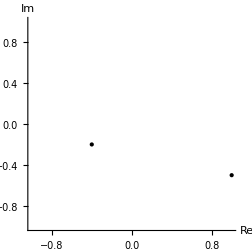

Также с помощью команды Arrow[{{x1,y1},{x2,y2}}] можно построить вектор

```mathematica
Graphics[{Arrow[{{0,0},ReIm[#]}]},Axes->True,AxesLabel->{Re,Im},PlotRange->{{-.5,.5},{-.5,.5}}]&[w[1-I/2]]
```

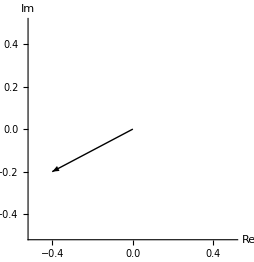

##### Пример №11.42

Найти и построить все значения следующей функции в указанной точке:

w=z+z^(1/4),z_0=-1

Для того чтобы найти все значения данной функции, воспользуемся экспоненциальной формой записи комплексного числа:

z=|z|ⅇ^(i(ϕ+2πk))

Функция корень 4-ой степени на комплексной плоскости имеет 4 корня, которые можно найти следующим образом:

z_k=|z|^(1/4)ⅇ^(ⅈ(ϕ/4+2/4 π k)), где k принимает значения -k=0,1,2,3

Запишем 4 корня, получающиеся в результате вычисления функции w(z_0):

```mathematica
z=Table[-1+Exp[I(Pi/4+Pi k/2)],{k,0,3}]
```

{-1+ⅇ^((ⅈ π)/4),-1+ⅇ^((3 ⅈ π)/4),-1+ⅇ^(-(3 ⅈ π)/4),-1+ⅇ^(-(ⅈ π)/4)}

Применим к каждому элементу списка функцию ReIm:

```mathematica
z=ReIm[z]
```

{{-1+1/(√2),1/(√2)},{-1-1/(√2),1/(√2)},{-1-1/(√2),-1/(√2)},{-1+1/(√2),-1/(√2)}}

Теперь изобразим 4 вектора данных точек и подпишем их с помощью команды Text[текст, {x,y}]:

```mathematica
Graphics[{Text[#,#],Arrow[{{0,0},#}]}&/@#,Axes->True,PlotRange->{{-2,1},{-1,1}},AxesLabel->{Re,Im}  ]&@z
```

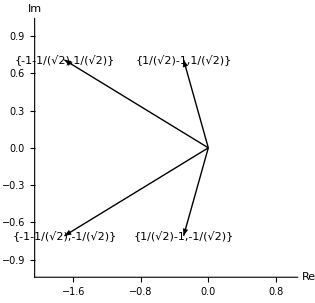

### 1.2. Основные элементарные функции комплексной переменной.

Следующие функции (как однозначные, так и многозначные) называются основными элементарными:

1. Дробно-рациональная функция

(a_0 z^n+a_1 z^(n-1)+...+a_n)/(b_0 z^m+b_1 z^(m-1)+...+b_m), n,m∈ℕ

Частными случаями этой функции являются:

а) линейная функция

a z+b, a,b∈ℂ, a≠ 0

б) степенная функция

z^n, n∈ℕ

в) дробно-линейная функция

(a z+b)/(c z+d), a,b,c,d∈ℂ, c≠ 0, a d-b c≠ 0

г) функция Жуковского

1/2(z+1/z)

2. Показательная функция

ⅇ^z=ⅇ^x(cos y+ⅈ sin y)

3. Тригонометрические функции

sin z=1/(2ⅈ)(ⅇ^(i z)-ⅇ^(-ⅈ z)), cos z=1/2(ⅇ^(i z)+ⅇ^(-ⅈ z)),
tg z=(ⅇ^(i z)-ⅇ^(-ⅈ z))/(ⅈ (ⅇ^(i z)+ⅇ^(-ⅈ z))),ctg z=(ⅈ(ⅇ^(i z)+ⅇ^(-ⅈ z)))/(ⅇ^(i z)-ⅇ^(-ⅈ z))

4. Гиперболические функции

sh z=1/2(ⅇ^z-ⅇ^-z),  ch z=1/2(ⅇ^z+ⅇ^-z),
th z =(sh z)/(ch z),     cth z=(ch z)/(sh z)

5. Логарифмическая функция

Ln z=ln |z| + ⅈ (arg z +2k π)

Функция Ln z является многозначной. В каждой точке z, отличной от нуля и ∞, она принимает бесконечно много значений. Выражение ln|z|+ⅈ arg z называется главным значением логарифмической функции и обозначается через ln z. Таким образом,

Ln z=ln z +2 k π ⅈ

6. Общая степенная функция

z^a=e^(a Ln z), a∈ℂ

Эта функция многозначная, ее главное значение равно ⅇ^(a ln z). Если a=1/n, где n∈ℕ, то получаем многозначную функцию - корень n-ой степени из комплексного числа:

z^(1/n)=ⅇ^(1/n(ln |z|+ⅈ( arg z +2 k π)))=(|z|)^(1/n)ⅇ^(ⅈ (arg z+2 k π)/n)

7. Общая показательная функция

a^z=ⅇ^(z Ln a), a∈ℂ

Главное значение этой многозначной функции равно ⅇ^(z ln a). В дальнейшем при a>0 полагаем a^z=ⅇ^(z ln a).

8. Обратные тригонометрические

Arccos z=-ⅈ Ln (z+√(z^2-1)),Arcsin z=-ⅈ Ln (ⅈ z+√(-z^2+1))
Arctg z=-ⅈ/2 Ln ((1+ⅈ z)/(1-ⅈ z))

##### Пример №11.53

Выделить действительную и мнимую части следующей функции:

w=ⅇ^(1-z)

Запишем z, используя алгебраическую форму записи комплексного числа:

```mathematica
z=x+I y;
```

Теперь воспользуемся функцией ComplexExpand, чтобы получить разложение заданной функции w:

```mathematica
ComplexExpand[Exp[1-z]]
```

ⅇ^(1-x) Cos[y]-ⅈ ⅇ^(1-x) Sin[y]

Итак получили, что:

u(x,y)=ⅇ^(1-x)cos y - действительная часть

v(x,y)=-ⅇ^(1-x)sin y - мнимая часть

##### Пример №11.55

Выделить действительную и мнимую части следующей функции:

w=sin (z-ⅈ)

Воспользуемся той же командой:

```mathematica
ComplexExpand[Sin[z-I]]
```

Cosh[1-y] Sin[x]-ⅈ Cos[x] Sinh[1-y]

Получили, что действительная и мнимая части равны:

u(x,y)=ch (1-y) sin x    
v(x,y)=-sh (1-y) cos x

##### Пример №11.62

Вычислить значения функции в указанной точке:

cos(z),z=1+ⅈ

Если вычислить значение косинуса в точке:

```mathematica
Cos[1+I]
```

Cos[1+ⅈ]

то видно, что Mathematica самостоятельно не преобразует выражения. Значит, если мы хотим получить ответ в другой форме, то нам необходимо воспользоваться преобразующими функциями. В данном случае - это ComplexExpand:

```mathematica
Cos[1+I]//ComplexExpand
```

Cos[1] Cosh[1]-ⅈ Sin[1] Sinh[1]

Итак, получили, что:

cos(1+ⅈ)=cos(1) ch(1)-ⅈ sin(1) sh(1)

##### Пример №11.65

Вычислить значения функции в указанной точке:

Ln(z), z=-1

В системе Wolfram Mathematica функция натурального логарифма имеет вид Log[a]. Она принимает в том числе и комплексные значения. Попытаемся найти значение логарифма от -1:

```mathematica
Log[-1]
```

ⅈ π

Мы получили главное значение логарифма, т.е. функция логарифма в системе Mathematica определена как:

Log[z]↔ln (z)

Чтобы получить множество значений функции Ln(z), необходимо к функции ln(z) добавить 2 π k ⅈ:

```mathematica
Log[-1]+2Pi k I//Factor
```

ⅈ (1+2 k) π

В итоге получаем ответ:

Ln(-1)=ⅈ π(1+2k)

##### Пример №11.75

Найти значение модуля и главное значение аргумента заданной функции в указанной точке:

w=sin z,  z=π+ⅈ ln3

Найдем значение функции в точке z и обозначим его за w:

```mathematica
w=Sin[Pi+I Log[3]]
```

-(4 ⅈ)/3

Теперь в рамках условия задачи воспользуемся функцией Abs[z], чтобы найти абсолютное значение (модуль) переменной w:

```mathematica
Abs[w]
```

4/3

Затем используем функцию Arg[z], чтобы найти аргумент числа w:

```mathematica
Arg[w]
```

-π/2

Итак, ответ:

|w|=|sin (π +ⅈ ln 3)|=4/3
arg w= arg sin (π +ⅈ ln 3)=-π/2

##### Пример №11.80

Найти все значения степени:

(-1)^ⅈ

По определению общая показательная функция задана, как:

a^z=ⅇ^(z Ln a)

Используя результат задачи 11.65, приходим к выводу, что:

(-1)^ⅈ=ⅇ^(i Ln(-1))=ⅇ^(ⅈ ⅈ π(1+2k))=ⅇ^(-π(1+2k)), где k∈ℤ

##### Пример №11.87

Решить уравнения:

ⅇ^(ⅈ z)-1=0

Для решения уравнений и неравенств в системе Wolfram Mathematica есть очень удобная функция - Solve[выражение, список переменных/функций],с которой каждый, кто работал ранее в Mathematica, конечно, должен быть знаком. Воспользуемся ей, чтобы получить решение исходного уравнения:

```mathematica
Solve[Exp[z]-I==0,z]
```

{{z→ConditionalExpression[(ⅈ π)/2+2 ⅈ π C[1],C[1]∈Integers]}}

Во-первых, обратим внимание на форму ответа - список из списков. Во-вторых, если функция-решение периодическая, то будут сгенерированы постоянные (C[1]), и при помощи функции ConditionalExpression будут указанны условия. Здесь - C[1] принадлежит множеству целых чисел (Integers). Чтобы получить само выражение-ответ, можно воспользоваться оператором “/.” :

```mathematica
z/.Solve[Exp[z]-I==0,z]
```

{ConditionalExpression[(ⅈ π)/2+2 ⅈ π C[1],C[1]∈Integers]}

Однако предварительно необходимо “сгладить” глубину вложенных списков:

```mathematica
z/.Flatten[Solve[Exp[z]-I==0,z]]//Factor
```

ConditionalExpression[1/2 ⅈ π (1+4 C[1]),C[1]∈Integers]

В дальнейшем всем этим операциям дополнительного внимания уделяться не будет.

Итак, ответ:

z=1/2 ⅈ π (1+4 k), k∈ℤ

### 1.3. Предел и непрерывность функции комплексной переменной.

Число A≠∞ называется пределом функции f(z) при z→ z_0 и обозначается A=lim_(z→z_0) f(z), если для любого ϵ>0 найдется δ(ϵ)>0 такое, что для всех z≠z_0, удовлетворяющих неравенству |z-z_0|< δ(ϵ), выполняется неравенство |f(z)-A|≤ ϵ. Либо, записывая символьным языком:

lim_(z→z_0) f(z)=A ⟺ ∀ϵ>0  ∃δ(ϵ)>0:∀z: |z-z_0|< δ(ϵ): |f(z)-A|≤ ϵ

Говорим, что lim_(z→z_0) f(z)=∞, если для любого R>0 найдется δ=δ(R)>0 такое, что для всех z≠z_0 таких, что|z-z_0|< δ(R), выполняется неравенство: |f(z)| >R.

Функция f(z) называется непрерывной в точке z_0, если она определена в этой точке и f(z_0)=lim_(z→z_0) f(z).

Функция f(z), непрерывная в каждой точке области D, называется непрерывной в этой области. Или на языке символов:

f(x) непрерывна в D ⟺ ∀z_i∈D: f(z_i)=lim_(z→z_i) f(z)

Функция f(z) называется равномерно непрерывной в области D, если для любого ϵ>0 найдется δ(ϵ)>0 такое, что для любых точек z_1 и z_2 из области D таких, что |z_1-z_2|< δ(ϵ), выполняется неравенство |f(z_1)-f(z_2)|<ϵ.

##### Пример №11.92

Вычислить предел:

lim_(z→ ⅈ) (z^2-4ⅈ z -3)/(z-ⅈ)

Для вычисления предела в Wolfram Mathematica существует функция Limit[ f(z), z→ z_0 ], которая, разумеется, автоматически применяет все правила нахождения предела. Воспользуемся ею:

```mathematica
Limit[(z^2-4I z-3)/(z-I),z-> I]
```

-2 ⅈ

В итоге:

lim_(z→ ⅈ) (z^2-4ⅈ z -3)/(z-ⅈ)=-2 ⅈ

Примечание: в будущем дополнительное внимание функции Limit уделяться не будет.